# Towards Universal Robotics

Douw Marx

University of Pretoria

Background: A universal robot is one that can perform any action that any other robot can. In this investigation, a universal robot is considered to be one that can rearrange its configuration to apply a given force at a given location. 

Overview: In this project, each of the criteria that are considered to be a requirement for universal robotics is investigated through a series of simulations. This involves using modular components to create an arbitrary motion, being able to resist or apply an arbitrary force and being capable of universal computation.

## Wolfram Community Post (material for blog post)

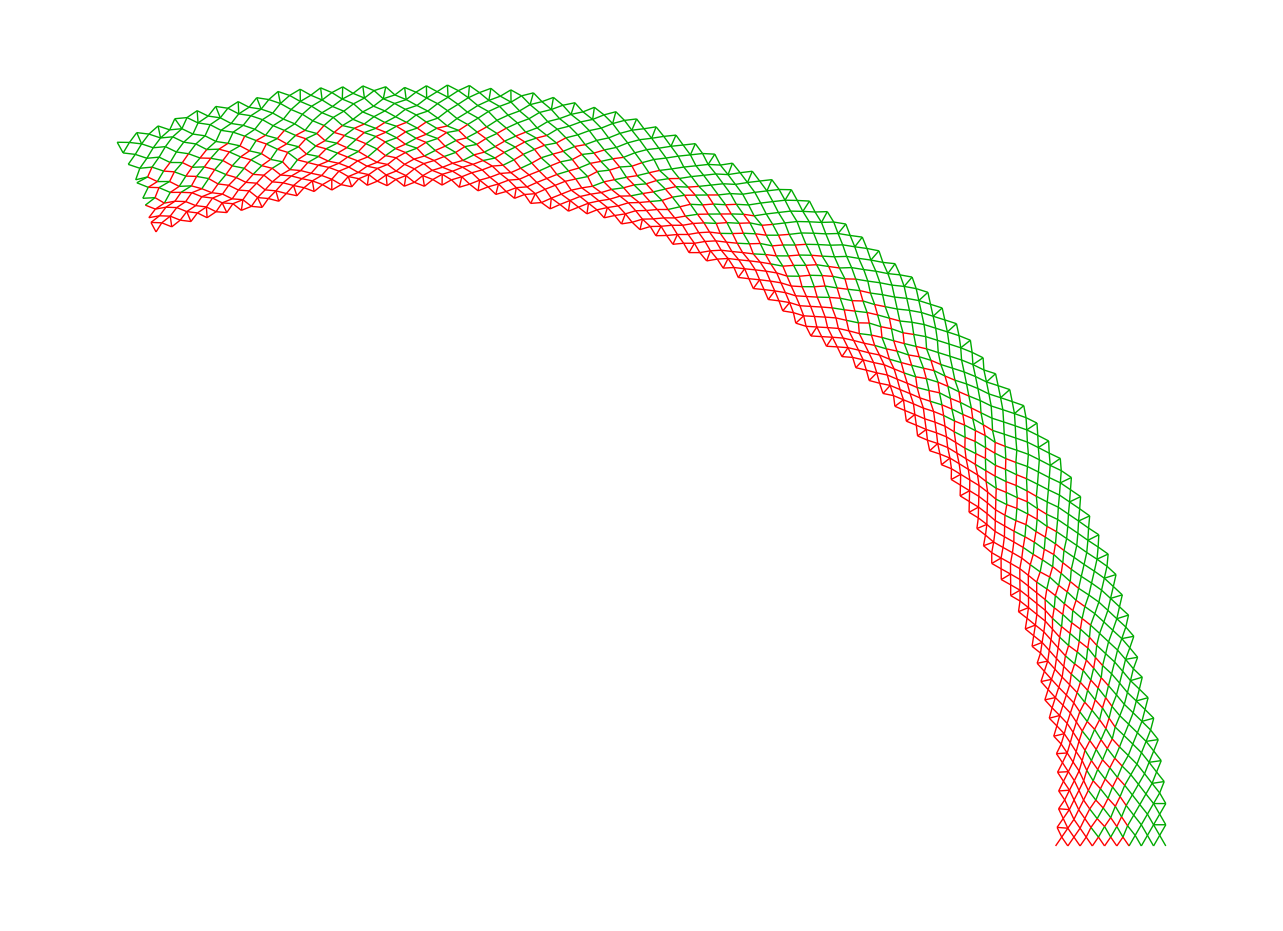

### What is Universal Robotics?

Universal computation or the ability to perform different tasks with the same underlying computer construction, simply by programming it differently, is a crucial part of what our world is today. The electronic device you are using to read this can (for the most part) be considered to be a universal computer.  What do we require to achieve the same sort of universality in the world of robotics? Is there a way that we can simulate the function of any currently existing robot with a set of identical robotic modules by simply “programming” it differently?

#### Parallel between universal computing and universal robotics.

Robotics can be compared with computation with a few possible examples.

Characteristic | Computation | Robotics
Fundamental Building Block | transistors,
vacuum tubes | linear actuators,
rotating actuators
Function of Fundamental
Building Block | boolean logic,
Three-valued logic | continuous motion,
 discrete motion
Interconnection of fundamental 
building blocks | A program | A robot

As a parallel to the world of universal computation, it is hypothesized that a series of simple robotics modules could be combined to replicate the function of any other robot.

#### Criteria for universal robotics

In order to investigate the possibility of general robotics, a criteria for determining when general robotics is achieved needs to be established. In this project, it is argued that the following three characteristics are required to achieve general robotics:

Ability to control the motion of points in space

Ability to resist or apply an arbitrary force at  at a specific position

Be capable of universal computation as a mean of controlling the robot.

It is anticipated that, in the same way that the extent of universality of a digital computer is for instance limited by the amount of memory it has, a universal robot would also have limitations based on each of the criteria listed above.

#### Overview

This post discusses each of the criteria for universal robotics as defined above. This includes sections on achieving arbitrary motion, resisting or applying arbitrary force and computational universality.

### Arbitrary Motion

One of the goals of robotics is to move a point (or multiple points) called the end-effector, along a prescribed path. Depending on the application, it might be necessary to prescribe both the desired position and angular orientation of the end-effector. In the context of robotics, this leads to either a inverse problem: “how should the state of the respective modules change in order to move the end effector on a desired path?” or the forward problem: “How does the position of the end effector change when changing the respective module states?”

#### Inverse Kinematics

A traditional methods for determining what the required module states for a given end effector location should is inverse kinematics. This involves solving a optimisation problem. The optimal actuator states are found for the desired end effector position, allowable maximum and minimum module states and collision constraints.

As an example, consider a 2D robot consisting of a triangular lattice of modules connected with joints that permit rotation. A sinusoidal path is traced by the end effector without extending or contracting the modules longer or shorter than their allowable maximum or minimum lengths.

```mathematica
ListAnimate[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

Solving the inverse problem becomes significantly harder as the number of modules (unknowns) increase.

#### Discrete Robotics and State Transition Diagrams

The forward problem involves simulating the end effector location for a set of module states.

As an example, possible states for a robot consisting of a triangular lattice of modules  having one of 2 possible states (60% ->100%) and its end-effector location is shown below.

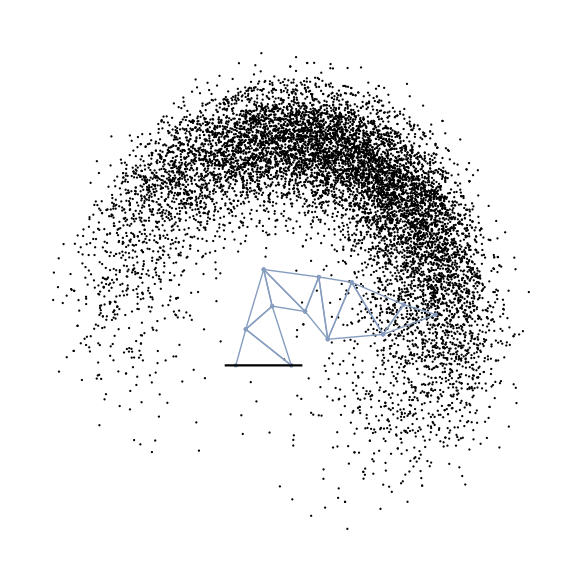

Continuous motion could be approximated by a sufficient amount of appropriately connected modules.

Notice that there are certain transitions between states that are not allowed. For instance, in the example below, the robot collides with itself. Other constraints could include collisions with the robots’ surroundings , exceeding the maximum force a module could resist or exert and transitions that are impossible without  going to a different state first.

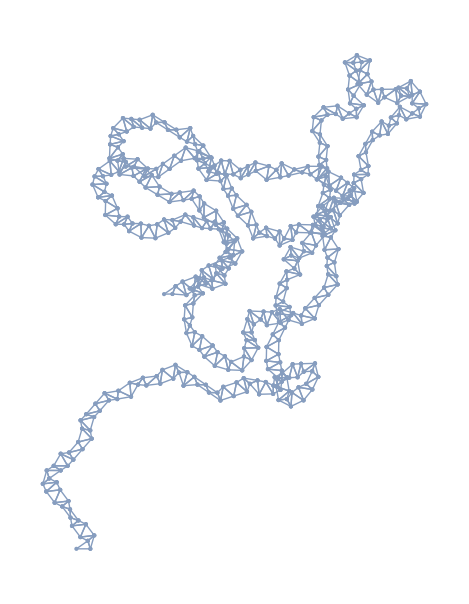

As an example of a state transition diagram, consider a robot that is allowed to change the length of single actuator at every time step. Notice that there are different paths to transition from one state to another.
-Graphics-

For instance,  the shortest path in transitioning between two states are shown below. Notice that only a single module changes state with each time-step.

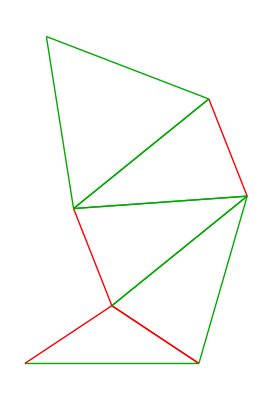
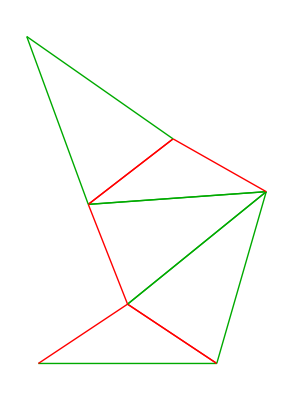
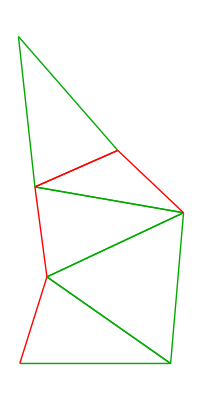
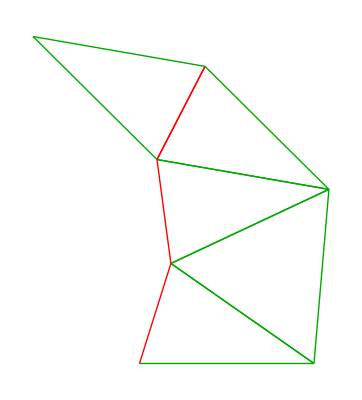
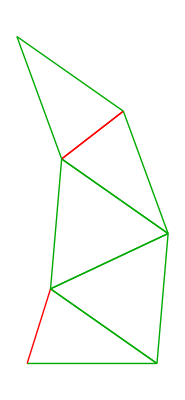
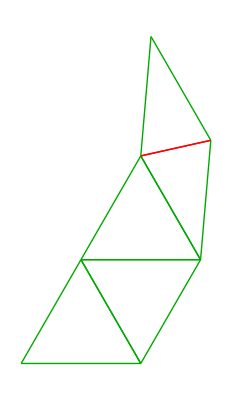
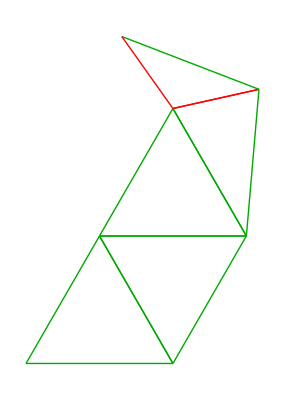
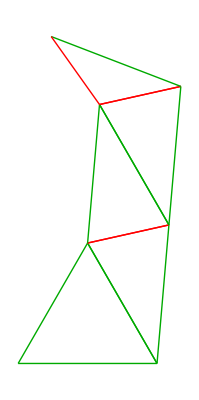

#### Rule-based Position control

An interesting opportunity for robot position control presents itself when working with robots that consist of modules with discrete states. Consider a 1D example where a module could either be long or short. The state of module is determined by a set a simple local rules. These rules consider the current state of a module and the state of its neighbours and determines the modules’ state at the next time step.

```mathematica
RodRule[rule_]:=Join[MapThread[Rule,{Join[Prepend[2]/@Tuples[{0,1},2],Tuples[{0,1},3],Append[2]/@Tuples[{0,1},2]],IntegerDigits[rule-1,2,16]}],{{2,2,0}->2,{2,2,1}->2,{0,2,2}->2,{1,2,2}->2}]
Row[Framed@Column[{Row[#1],#2}/.{0->White,1->Black,2->Darker@Red},Center]&@@@RodRule[50845]]
```

RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]GrayLevel[1]
GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]GrayLevel[0]
GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]GrayLevel[1]
GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]GrayLevel[0]
GrayLevel[1]GrayLevel[1]GrayLevel[1]GrayLevel[1]
GrayLevel[1]GrayLevel[1]GrayLevel[1]GrayLevel[0]
GrayLevel[0]GrayLevel[1]GrayLevel[0]GrayLevel[1]
GrayLevel[0]GrayLevel[1]GrayLevel[0]GrayLevel[0]
GrayLevel[1]GrayLevel[0]GrayLevel[1]GrayLevel[1]
GrayLevel[0]GrayLevel[0]GrayLevel[1]GrayLevel[0]
GrayLevel[1]GrayLevel[0]GrayLevel[0]GrayLevel[1]
GrayLevel[1]GrayLevel[0]GrayLevel[0]GrayLevel[0]
GrayLevel[0]GrayLevel[1]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[0]GrayLevel[1]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[0]GrayLevel[0]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]GrayLevel[0]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]
RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]
RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]
RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]
RGBColor[Rational[2, 3], 0, 0]

The set of rules above (red=boundary,white=short, black=long) is chosen as its behaviour appears near random. This is necessary since this ensures that most of the possible states that the robot can be in can be reached within a relatively small amount of updates of the rule. By applying the set of rules a fixed number of times from the initial condition (all short modules) the robot can be extended to a known length. Since the rate at which the rule updating could occur is orders of magnitude faster than the dynamics of the system, the robot would only respond after the desired number of rule updates were performed. The robot can then be reset to its initial condition and the rules re-applied to transition to the next desired state.

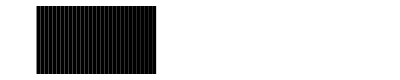
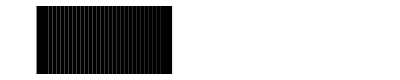
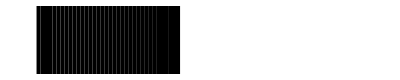
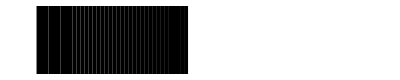
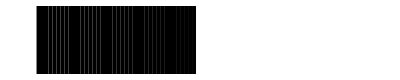
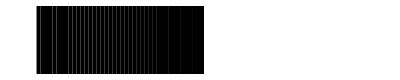
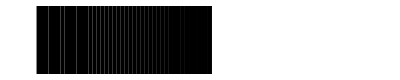
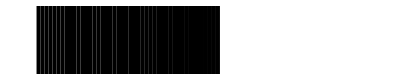
```mathematica
ListAnimate[{{{"Apply rule 0 times"}, {-Graphics-}},{{"Apply rule 1 times"}, {-Graphics-}},{{"Apply rule 2 times"}, {-Graphics-}},{{"Apply rule 3 times"}, {-Graphics-}},{{"Apply rule 29 times"}, {-Graphics-}},{{"Apply rule 4 times"}, {-Graphics-}},{{"Apply rule 5 times"}, {-Graphics-}},{{"Apply rule 576 times"}, {-Graphics-}},{{"Apply rule 10 times"}, {-Graphics-}},{{"Apply rule 13 times"}, {-Graphics-}},{{"Apply rule 44 times"}, {-Graphics-}},{{"Apply rule 8 times"}, {-Graphics-}},{{"Apply rule 9 times"}, {-Graphics-}},{{"Apply rule 15 times"}, {-Graphics-}},{{"Apply rule 11 times"}, {-Graphics-}},{{"Apply rule 25 times"}, {-Graphics-}},{{"Apply rule 18 times"}, {-Graphics-}},{{"Apply rule 33 times"}, {-Graphics-}},{{"Apply rule 17 times"}, {-Graphics-}},{{"Apply rule 27 times"}, {-Graphics-}},{{"Apply rule 47 times"}, {-Graphics-}},{{"Apply rule 16 times"}, {-Graphics-}},{{"Apply rule 65 times"}, {-Graphics-}},{{"Apply rule 215 times"}, {-Graphics-}},{{"Apply rule 63 times"}, {-Graphics-}},{{"Apply rule 1885 times"}, {-Graphics-}}},3]
```

### Arbitrary Force

For a robot to perform a certain task its has to be able to resist the forces that are applied to it. Even in the case where a robot does not have the function of exerting a force, the force of gravity on the robot should  be resisted. A few of the factors that could influence a modular robots’ ability to apply an arbitrary force include

There is a maximum force that each of the modules can resist or apply

The interconnected lattice of modules should be rigid

As many as possible modules should contribute to resisting the applied force

Two example lattices that could be scaled up to hypothetically apply or resist and arbitrary force is shown below. The lattice is rigid if the lower joint of all the lowest modules are fixed to ground.

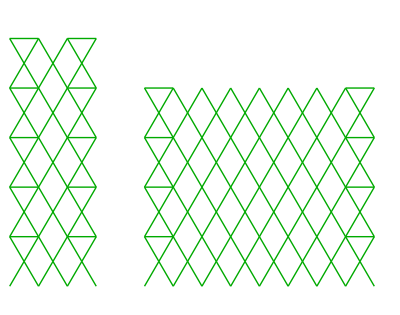

By increasing the number of columns, the number of modules that act in parallel increase and as a result, the applied force (or moment it causes) that can be resisted increases. To prove this, the forces in the truss-like robot would have to be calculated. We can then check that the tensile or compression forces in the respective modules do not exceed their maximum allowable value. 
It should also be mentioned that the example shown here is not statically determinate  (number of members + number of fixed degrees of freedom - 2xnumber of joints =0) and a triangular lattice that distributes the force applied at the end effector through the structure would have to be added to make used of all added columns in resisting a larger force.

The examples below show how the combination of fundamental building blocks could be combined to create a more complicated fundamental building block. For instance, in the left side picture a left turn is created by stacking a series of wedge shaped layers which in turn was created by simple linear actuator modules that can either be long or short. This more complex “left turn”, “long” or “short” building block can then be used to construct a an even more complex structure as in the right side picture.

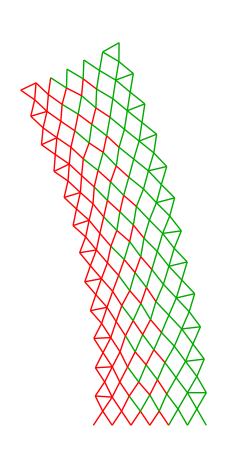
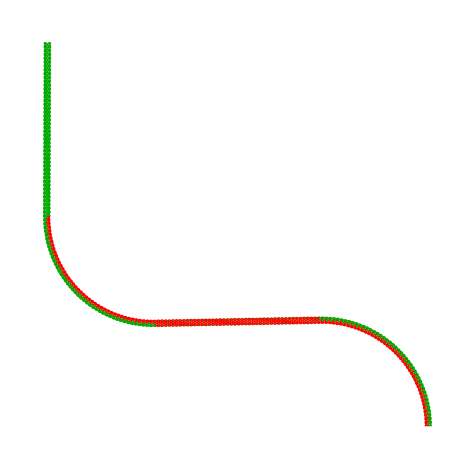

### Universal Computation

To investigate universal computation in the context of robotics, a one-dimensional problem is considered:

A robot consists of serially connected modules that are capable of extending and contracting.

The modules can take one of two states, long or short.

Local rules determine what the state of a module would be in the next time step. For instance, if the neighbours of certain currently short module are both long, the rule might stipulate that this module should be long in the following state.

At every time-step, before the local rules are applied, an additional module in the “short” state is added to the robot. One can think of the robot as systematically being assembled from one side.

There are 2^16 = 65536 possible rules that could define the behaviour of this sort of one-dimensional robot. Looking at the evolution of theses rules, a few rules show behaviour that could indicate that this system could be capable of universal computation. 

For example, consider rule 51051

```mathematica
rule51051 = ;
Row[Framed@Column[{Row[#1],#2}/.{0->White,1->Black,2->Darker@Red},Center]&@@@rule51051]
```

RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]GrayLevel[1]
GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]GrayLevel[0]
GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]GrayLevel[1]
GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]GrayLevel[0]
GrayLevel[1]GrayLevel[1]GrayLevel[1]GrayLevel[1]
GrayLevel[1]GrayLevel[1]GrayLevel[1]GrayLevel[0]
GrayLevel[0]GrayLevel[1]GrayLevel[0]GrayLevel[1]
GrayLevel[0]GrayLevel[1]GrayLevel[0]GrayLevel[0]
GrayLevel[0]GrayLevel[0]GrayLevel[1]GrayLevel[1]
GrayLevel[1]GrayLevel[0]GrayLevel[1]GrayLevel[0]
GrayLevel[0]GrayLevel[0]GrayLevel[0]GrayLevel[1]
GrayLevel[0]GrayLevel[0]GrayLevel[0]GrayLevel[0]
GrayLevel[1]GrayLevel[1]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[0]GrayLevel[1]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]GrayLevel[0]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[0]GrayLevel[0]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]
RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]
RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]
RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]
RGBColor[Rational[2, 3], 0, 0]

Red indicate boundaries, white indicate modules in short state and black indicate modules in long state.

The evolution of the robot are shown below. Notice that the number of modules that the robot is made up of grows with every update. The states of the modules short/long are shown with white and grey and the boundary is shown as black .  Note that the figure does not show the actual length of the 1D robot, but rather the states of the modules over time.  Colliding gliders, as found in the Turing complete rule 110 elementary cellular automata (ECA110) is visible.

```mathematica
nevol = 1000;init={2,0,1,0,2};
evol51051 = NestList[Last@CellularAutomaton[rule51051,Join[{2,0},#[[2;;-1]]],1]&,init,nevol];
ArrayPlot[evol51051]
```

-Graphics-

In fact, any of the elementary cellular automata could be simulated in this way. If the boundary rules are set appropriately an all white background can be generated at every time step. As an example, we can simulate ECA 110 with rules below using the 1D robot example.

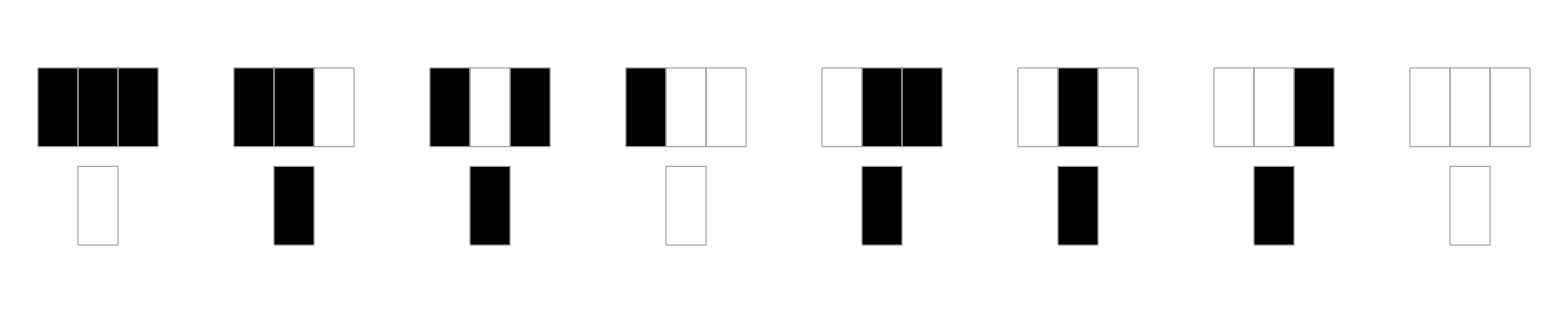

```mathematica
RulePlot[CellularAutomaton[110]]
```

We define the rules for the 1D robot to be the same as ECA 110 apart from the rules that generate the all-white background

```mathematica
module110 = ;
Row[Framed@Column[{Row[#1],#2}/.{0->White,1->Black,2->Darker@Red},Center]&@@@module110]
```

RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]GrayLevel[1]
GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]GrayLevel[0]
GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]GrayLevel[1]
GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]GrayLevel[0]
GrayLevel[1]GrayLevel[1]GrayLevel[1]GrayLevel[1]
GrayLevel[1]GrayLevel[1]GrayLevel[1]GrayLevel[0]
GrayLevel[0]GrayLevel[1]GrayLevel[0]GrayLevel[1]
GrayLevel[0]GrayLevel[1]GrayLevel[0]GrayLevel[0]
GrayLevel[0]GrayLevel[0]GrayLevel[1]GrayLevel[1]
GrayLevel[1]GrayLevel[0]GrayLevel[1]GrayLevel[0]
GrayLevel[0]GrayLevel[0]GrayLevel[0]GrayLevel[1]
GrayLevel[0]GrayLevel[0]GrayLevel[0]GrayLevel[0]
GrayLevel[1]GrayLevel[1]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]GrayLevel[1]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]GrayLevel[0]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]GrayLevel[0]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]
GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]
RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]
RGBColor[Rational[2, 3], 0, 0]GrayLevel[1]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]
RGBColor[Rational[2, 3], 0, 0]GrayLevel[0]RGBColor[Rational[2, 3], 0, 0]RGBColor[Rational[2, 3], 0, 0]
RGBColor[Rational[2, 3], 0, 0]

When plotting a left-zero-padded version of the 1D robot result, we can recognize the well known ECA 110 state evolution

```mathematica
nevol = 1000;init={2,0,1,0,2};
evol = PadLeft[NestList[Last@CellularAutomaton[module110,Join[{2,0},#[[2;;-1]]],1]&,init,nevol]];
ArrayPlot[evol]
```

-Graphics-

We can prove that the evolution of the 1D robot example is the same as ECA110

```mathematica
evolrem2 = evol/. 2->0 ;  (*Repalce the boundaries (2) with 0's*)
 evolrem2[[2;;-2,3;;-3]]==CellularAutomaton[110,{{1},0},nevol][[3;;-1,All]] (*Make sure the shapes allign*)
```

True

Generalizing to 2 and 3 dimensions, it is conceivable that a modular robot with an arbitrary function could be constructed by the updating of simple rules. After a certain number of rule updates and module additions the robot would be built. In order for the robot just constructed to perform its desired function, the local rules that govern its current state could then be updated each time it has to perform a certain function.

### Simplifications and Alternatives

Notice that many simplification and assumptions were made in this project. The project should be viewed as a preliminary investigation into what universal robotics could mean and it is not implied that any of the simulations in this post are physically realizable.

### Acknowledgement

Mentor: Philip Maymin
Thank you for everything that you taught me during this summer school.

For the full project notebook an supporting packages, please visit www.notebookarchive  or https://github.com/DouwMarx/wolfram_summer_school

## Complete project work

### If we are working with a triangular lattice, there are one of two possible next two points based on the current given rod lengths

```mathematica
coord1 = {0,0};coord2={1,0};
length1 = 1;
length2 = 1.2;
coord3 = ThirdCoord[coord1,coord2,length1,length2]
```

{0.28,0.96}

#### Plotting one of the possible resulting triangular components

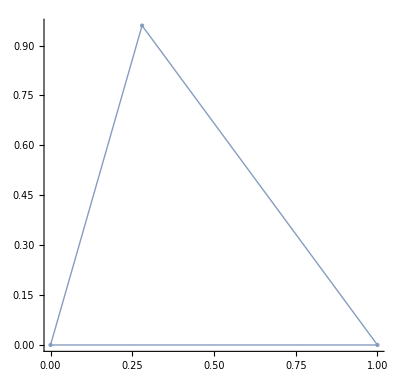

```mathematica
MeshTriag[coord1,coord2,coord3,Automatic]
```

#### Combining a few triangular building blocks with random module lengths between 0.6 and 1.0

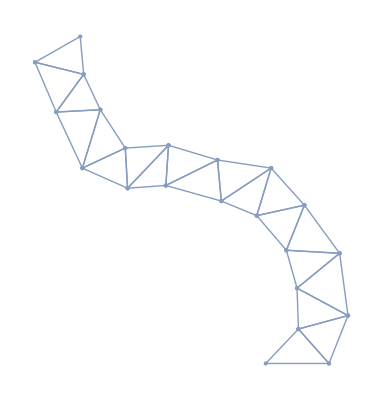

```mathematica
nfreepoints =20;
fixed1 = {0,0};
fixed2 = {1,0};
lens = RandomReal[{0.6,1},nfreepoints*2];
triagworm = MakeTriangleWorm[fixed1,fixed2,lens];

MeshAllTriag[triagworm,Automatic]
```

### The inverse problem: What should the module lengths be to move the mechanism in a certain way?

Define a structure and find the coordinates of the nodes in terms of the module lengths

```mathematica
nfreepoints = 5;
nunknowns = nfreepoints*2;
lattice =MakeSymbolicTriangleWorm[fixed1,fixed2,nfreepoints];
endeffector = lattice[[-1]];
```

The y-coordinate for the final point in the lattice as a function of the module lengths is for instance given as

```mathematica
Style[endeffector[[2]],Small]
```

len1 √(1-((1+len1^2-len2^2)^2)/(4 len1^2))+len5 Sin[1]+len9 Sin[ArcCos[(-len10^2+len9^2+(1/2 (1)+1-len7 1)^2+len7^2 Sin[ArcCos[1/1]+ArcTan[1]]^2)/(2 len9 √((1/2 (1+len1^2-len2^2)+1/2 (1)-len7 Cos[1])^2+len7^2 Sin[ArcCos[1]+1]^2))]+ArcTan[1/2 (1+len1^2-len2^2)+1/2 (1)+len7 Cos[ArcCos[1/(2 len7 √1)]+ArcTan[1,1]],1]]
 |  |  |  |

We now impose the constraint that the final point in the lattice should lay on a certain specified coordinate

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{len1→0.980243,len2→1.09127,len3→0.931496,len4→1.12499,len5→1.06206,len6→1.06673,len7→0.939417,len8→1.05861,len9→1.12598,len10→1.05918}

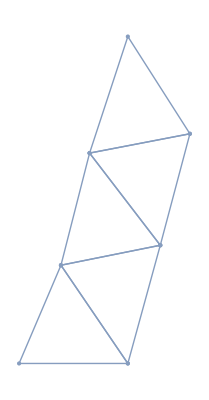

```mathematica
desired = {1,3};
endeffectorconstraints:= {Norm[endeffector-desired]};
constraints = Join[endeffectorconstraints];
sol = OptForDesired[constraints,MakeOptStartPoint[nunknowns]]
MeshAllTriag[lattice/.sol,Automatic]
```

Notice that in the previous example the modules could take any arbitrary length. Now imposing a constraint on the allowable lengths:

{0.6<len1<1,0.6<len2<1,0.6<len3<1,0.6<len4<1,0.6<len5<1,0.6<len6<1,0.6<len7<1,0.6<len8<1,0.6<len9<1,0.6<len10<1}

Optimisation Unsuccessfull, cost=0.191768

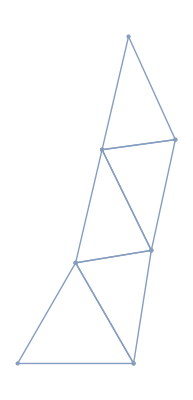

```mathematica
desired = {1,3};
endeffectorconstraints:= {Norm[endeffector-desired]};
modulelengthconstraint=MakeLengthConstraints[nunknowns,0.6,1]

constraints = Join[endeffectorconstraints,modulelengthconstraint];
sol = OptForDesired[constraints,MakeOptStartPoint[nunknowns]];
MeshAllTriag[lattice/.sol,Automatic]
```

In the above example the desired location could not be reached due to the length constraints.

#### Solving for a continuous path

```mathematica
path = Table[{i,2.0+ 0.3*Sin[15*i]},{i,0,1.2,0.01}];

optfordes = OptForDesired[constraints,MakeOptStartPoint[nunknowns]];

requiredlens = {optfordes};
Do[
endeffectorconstraints:= {Norm[endeffector-path[[j]]]};
modulelengthconstraint=MakeLengthConstraints[nunknowns,0.6,1];
constraints = Join[endeffectorconstraints,modulelengthconstraint];
optfordes =OptForDesired[constraints,SolAsStartPoint[optfordes]];
 AppendTo[requiredlens,optfordes],
{j,Length[path]-1}];
requiredlens;
```

Optimisation Unsuccessfull, cost=0.191768

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

```mathematica
a = Animate[MeshAllTriag[lattice/.requiredlens[[i]],{{0,2},{0,3}}],{i,Range[Length[path]-20]}]
```

```mathematica
a =Table[MeshAllTriag[lattice/.requiredlens[[i]],{{0,2},{0,3}}],{i,Range[Length[path]]}];
```

```mathematica
Export["C:\\Users\\douwm\\repos\\wolfram_summer_school\\videos\\2Dsinefirstcut.gif",a[[2;;-1]]]
```

C:\Users\douwm\repos\wolfram_summer_school\videos\2Dsinefirstcut.gif

```mathematica
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\2d_toolbox.wl"]
```

#### For a specific robot structure that consists only of triangles with no redundant modules and having one of 2 possible states for each module (long or short)

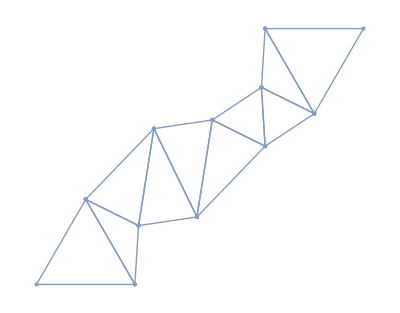

```mathematica
nrods =20;
shortlength = 0.6;
longlength = 1;
coords = MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]];
MeshAllTriag[coords,All]
```

#### If there are a large number of rods, collisions between rods tend to occur that can be detected

```mathematica
nrods =1000;
shortlength = 0.6;
longlength = 1;
coords = MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]];
Echo["Did a collision occur?"];
Echo[CollisionQ[coords,shortlength]];
MeshAllTriag[coords,All]
```

Did a collision occur?

True

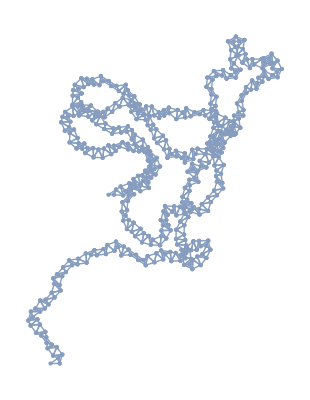

#### We can get an idea of the expected workspace of the mechanism (where the final point in the mechanism could go) by trying a series of random rod lengths

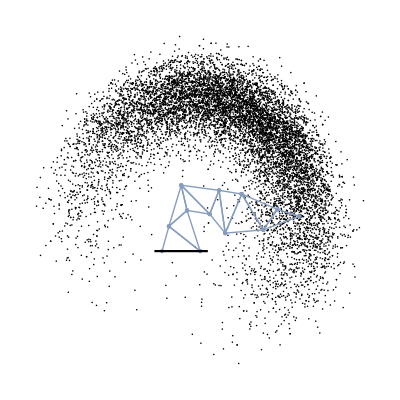

```mathematica
nrods =20;
shortlength = 0.6;
longlength = 1;
coords = Table[MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]],10000];
endeffector = coords[[All,-1,All]];
coords = MakeTriangleWorm[{0,0},{1,0}, RandomChoice[{shortlength,longlength},nrods]];
Show[ListPlot[Style[endeffector,Black],PlotRange->All,AspectRatio->1],MeshAllTriag[coords,All],ListLinePlot[Style[{{-0.2,0},{1.2,0}},Black]],Axes->False]
```

#### Transitioning from a random state to its neighbour and then its neighbours’ neighbours.

a possible state {initial condition}

{0.6,0.6,0.6,0.6,1,1,1,0.6,1,1,1,0.6,1,0.6,1,0.6,1,1,1,1,1,0.6,0.6,0.6,0.6,1,1,1,1,0.6,1,0.6,0.6,0.6,1,0.6,1,1,1,1,1,0.6,0.6,1,0.6,0.6,0.6,0.6,0.6,1}

initial condition neighbours

First neighbours' neighbours

{1,0.6,1,1,1,0.6,0.6,0.6,1,0.6,0.6,0.6}

a possible state {initial condition}

{0.6,0.6,1,1,1,0.6,0.6,1,1,0.6,1,1}

initial condition neighbours

(1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1
0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6)

First neighbours' neighbours

(0.6 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 1 | 0.6 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 0.6 | 1 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 0.6 | 0.6 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 1 | 1 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 0.6 | 1
1 | 0.6 | 1 | 1 | 1 | 0.6 | 0.6 | 1 | 1 | 0.6 | 1 | 0.6)

-Graphics-

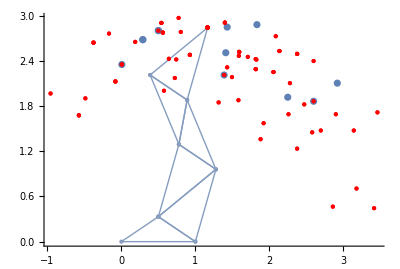

```mathematica
nc = MakeTriangleWorm[fixed1,fixed2,#]&/@ns;
nnc = MakeTriangleWorm[fixed1,fixed2,#]&/@Flatten[nns,1];
ne = nc[[All,-1,All]];
nne = nnc[[All,-1,All]];

g2 =Show[MeshAllTriag[MakeTriangleWorm[fixed1,fixed2,possiblestate],All],ListPlot[ne],ListPlot[nne,PlotStyle->{PointSize[Medium],Red}]]
```

#### Transition between all states

```mathematica
nrods=8;
shortlength=0.6;
longlength=1;
allstates=Tuples[{shortlength,longlength},nrods];
Graph[Flatten[StateToNeighbours[#,Black]&/@allstates]]
```

-Graphics-

```mathematica
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\packages\\force_toolbox.wl"]
```

```mathematica
clong = 3;(*Number of hourglass columns, c≥2*)
rlong =5; (*Number fo hourglass rows, r≥1*)
nrlong = (4*clong+2); (*Rods per row*)
nlong = nrlong*rlong ;

cshort = 5;(*Number of hourglass columns, c≥2*)
rshort =3; (*Number fo hourglass rows, r≥1*)
nrshort = (4*cshort+2); (*Rods per row*)
nshort = nrshort*rshort ;
long = 1;
short = 0.8;

rodlengths = ConstantArray[1,nlong];

Graphics[Join[Last@BuildStructure[clong,rlong,rodlengths]]]
```

Part::span: 1;;nr is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 3 of {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«20»}⟦1;;nr⟧ does not exist.

Part::partw: Part 4 of {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«20»}⟦1;;nr⟧ does not exist.

Part::span: 1;;nr is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 4 of {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«20»}⟦1;;nr⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::span: 1;;nr is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

$Aborted

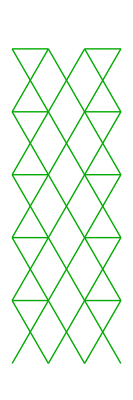

```mathematica
c = 3;(*Number of hourglass columns, c≥2*)
r =5; (*Number fo hourglass rows, r≥1*)
nr = (4*c+2); (*Rods per row*)
n = nr*r ;

rodlengths = ConstantArray[1,n];
(*Number of rods*)Graphics[Join[Last@BuildStructure[c,r,rodlengths]],PlotRange->{0,9}]
```

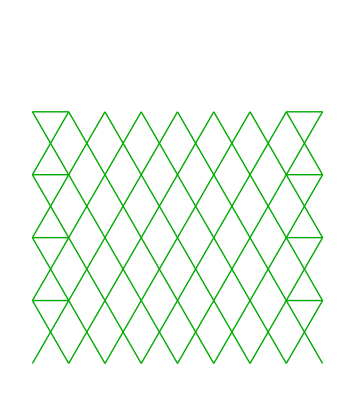

```mathematica
c = 8;(*Number of hourglass columns, c≥2*)
r =4; (*Number fo hourglass rows, r≥1*)
nr = (4*c+2); (*Rods per row*)
n = nr*r ;

rodlengths = ConstantArray[1,n];
(*Number of rods*)Graphics[Join[Last@BuildStructure[c,r,rodlengths]],PlotRange->{0,9}]
```

```mathematica
GraphicsRow[{-Graphics-,-Graphics-}]
```

-Graphics-

```mathematica
c = 3;(*Number of hourglass columns, c≥2*)
r =90; (*Number fo hourglass rows, r≥1*)
nr = (4*c+2); (*Rods per row*)
n = nr*r ;(*Number of rods*)
```

```mathematica
(*rodlengths = RandomChoice[{0.95,1},n];*)

long =1;
short =0.96;

(*leftturn = Join[ConstantArray[short,2*c/3],
ConstantArray[short,2*c/3],
ConstantArray[long,2*c/3],(*botrow*)
ConstantArray[short,2*c/3],
ConstantArray[long,2*c/3],(*midrow*)
{long,long},
{long,long}]; *)
leftturn = Join[ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[long,(nr-2)/6],(*botrow*)
ConstantArray[short,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6-1],(*midrow*)
{short,short},
{long,long}]; (*right hand top tip*)

rightturn = Join[ConstantArray[long,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],(*botrow*)
ConstantArray[long,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[short,(nr-2)/6-1],(*midrow*)
{long,long},
{short,short}]; (*right hand top tip*)

short = Join[ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],(*botrow*)
ConstantArray[short,(nr-2)/6-1],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6-1],(*midrow*)
{short,long},
{long,short}]; (*right hand top tip*)

long= Join[ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6],(*botrow*)
ConstantArray[long,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6-1],(*midrow*)
{long,long},
{long,long}]; (*right hand top tip*)

(*rodlengths= Join[leftturn,leftturn];*)
(*rodlengths= Join[rightturn,rightturn];*)
(*rodlengths= Join[short,short];*)

(*rodlengths= Flatten[RandomChoice[{leftturn,rightturn},r]];*)

(*rodlengths= Flatten[ConstantArray[leftturn,r]];*)
```

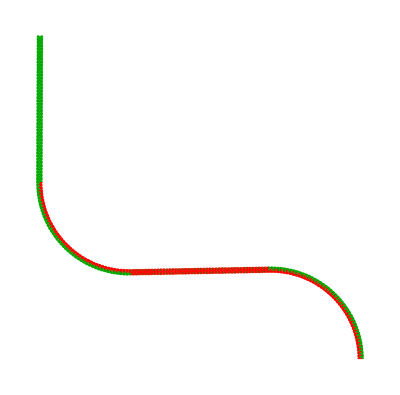

```mathematica
rodlengths= Flatten[Join[ConstantArray[leftturn,r/4],ConstantArray[short,r/4],ConstantArray[rightturn,r/4],ConstantArray[long,r/4]]];
Graphics[Join[Last@BuildStructure[c,r,rodlengths]]]
```

```mathematica
c = 9;(*Number of hourglass columns, c≥2*)
r =70; (*Number fo hourglass rows, r≥1*)
nr = (4*c+2); (*Rods per row*)
n = nr*r ;(*Number of rods*)
```

```mathematica
(*rodlengths = RandomChoice[{0.95,1},n];*)

long =1;
short =0.88;

(*leftturn = Join[ConstantArray[short,2*c/3],
ConstantArray[short,2*c/3],
ConstantArray[long,2*c/3],(*botrow*)
ConstantArray[short,2*c/3],
ConstantArray[long,2*c/3],(*midrow*)
{long,long},
{long,long}]; *)
leftturn = Join[ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[long,(nr-2)/6],(*botrow*)
ConstantArray[short,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6-1],(*midrow*)
{short,short},
{long,long}]; (*right hand top tip*)

rightturn = Join[ConstantArray[long,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],(*botrow*)
ConstantArray[long,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[short,(nr-2)/6-1],(*midrow*)
{long,long},
{short,short}]; (*right hand top tip*)

short = Join[ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6],(*botrow*)
ConstantArray[short,(nr-2)/6-1],
ConstantArray[short,(nr-2)/6],
ConstantArray[short,(nr-2)/6-1],(*midrow*)
{short,long},
{long,short}]; (*right hand top tip*)

long= Join[ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6],(*botrow*)
ConstantArray[long,(nr-2)/6-1],
ConstantArray[long,(nr-2)/6],
ConstantArray[long,(nr-2)/6-1],(*midrow*)
{long,long},
{long,long}]; (*right hand top tip*)

(*rodlengths= Join[leftturn,leftturn];*)
(*rodlengths= Join[rightturn,rightturn];*)
(*rodlengths= Join[short,short];*)

(*rodlengths= Flatten[RandomChoice[{leftturn,rightturn},r]];*)

(*rodlengths= Flatten[ConstantArray[leftturn,r]];*)
```

```mathematica
rodlengths= Flatten[Join[ConstantArray[leftturn,r]]];
Graphics[Join[Last@BuildStructure[c,r,rodlengths]]]
```

-Graphics-

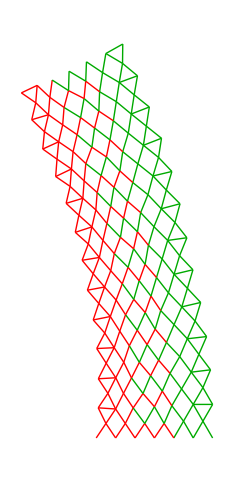

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

## Keywords

Robotics

Universality

Cellular Automata

Modular Robotics

## Acknowledgment

Mentor: Philip Maymin

## References